# Savage 1803.03326

```mathematica
imageRes = 250; (* image resolution for exporting images *)
```

## Lattice, Configuration, and Hamiltonian

Define a 1D lattice with periodic boundary conditions

```mathematica
L=4; (* number of spatial sites *)
nfs =2 L; (* number of fermion sites *)
```

```mathematica
ClearAll[fs]; 
fs[n_]:=Mod[n, nfs];
```

```mathematica
fs[nfs] == fs[0] (* check PBC *)
fs[-1] == fs[nfs-1]
```

True

True

```mathematica
lattice = Table[fs[n], {n, 0, nfs-1}]
```

{0,1,2,3,4,5,6,7}

Define the parameters of the model

```mathematica
ClearAll[a, g,w, J,m, m0, w0, J0];
a = 1.;
w0 = 1/(2a); (* fix that! a = 1 *)
(* Relevant dimless parameters are wrt w0 *)
j0w0 = 1.667;
m0w0 = 0.167;
w0t0 = 0.1;
(* the rest is determined *)
J0 = j0w0 w0;
m0 = m0w0 w0 ; 
t0 = w0t0 / w0;
g = 2 √(J0 w0); 
params = {J-> J0, w-> w0, m->m0};
```

## Define Truncation Parameters

```mathematica
Λ1 =1;   (* primary cutoff - absolute value of each link should not exceed this *)
Λ2 = 3; (* secondary cutoff - sum of squares of all links should not exceed this *)
Λ3 = 3; (* secondary cutoff for the building the smart operator *)
```

Define a Hamiltonian

```mathematica
Hhop = Sum[w SubPlus[σ][fs[n]].SubPlus[U][fs[n]].SubMinus[σ][fs[n+1]].Ket[Ψ] +w SubPlus[σ][fs[n+1]].SubMinus[U][fs[n]].SubMinus[σ][fs[n]].Ket[Ψ] ,{n,0, nfs-1}]
```

w σ_+[0].U_-[7].σ_-[7].Ψ+w σ_+[0].U_+[0].σ_-[1].Ψ+w σ_+[1].U_-[0].σ_-[0].Ψ+w σ_+[1].U_+[1].σ_-[2].Ψ+w σ_+[2].U_-[1].σ_-[1].Ψ+w σ_+[2].U_+[2].σ_-[3].Ψ+w σ_+[3].U_-[2].σ_-[2].Ψ+w σ_+[3].U_+[3].σ_-[4].Ψ+w σ_+[4].U_-[3].σ_-[3].Ψ+w σ_+[4].U_+[4].σ_-[5].Ψ+w σ_+[5].U_-[4].σ_-[4].Ψ+w σ_+[5].U_+[5].σ_-[6].Ψ+w σ_+[6].U_-[5].σ_-[5].Ψ+w σ_+[6].U_+[6].σ_-[7].Ψ+w σ_+[7].U_-[6].σ_-[6].Ψ+w σ_+[7].U_+[7].σ_-[0].Ψ

```mathematica
Hmass = Sum[m/2(-1)^n Subscript[σ, z][fs[n]].Ket[Ψ],{n,0, nfs-1}]
```

1/2 m σ_z[0].Ψ-1/2 m σ_z[1].Ψ+1/2 m σ_z[2].Ψ-1/2 m σ_z[3].Ψ+1/2 m σ_z[4].Ψ-1/2 m σ_z[5].Ψ+1/2 m σ_z[6].Ψ-1/2 m σ_z[7].Ψ

```mathematica
Hfield = Sum[J l[fs[n]].l[fs[n]].Ket[Ψ],{n,0, nfs-1}]
```

J l[0].l[0].Ψ+J l[1].l[1].Ψ+J l[2].l[2].Ψ+J l[3].l[3].Ψ+J l[4].l[4].Ψ+J l[5].l[5].Ψ+J l[6].l[6].Ψ+J l[7].l[7].Ψ

```mathematica
H =  Simplify[Hhop + Hmass + Hfield];
```

Define a basis in the required subspace

```mathematica
singleSpinBasis = {1,-1}; 
singleLinkBasis = Table[l, {l, -Λ1, Λ1}];
```

```mathematica
spinKets = Ket @@@ Select[Tuples[singleSpinBasis, nfs], Total[#]== 0 &] (* choose subspace with Q = 0 *)
```

{1,1,1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,1,1,-1,-1,1,-1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,-1,-1,-1,1,1,1,-1,1,1,-1,-1,-1,1,1,-1,1,-1,1,-1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,-1,1,1,-1,-1,1,-1,-1,1,1,1,-1,-1,-1,1,1,-1,1,1,-1,-1,-1,1,-1,1,1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,-1,1,-1,1,-1,1,1,-1,-1,-1,1,1,-1,1,-1,1,1,-1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,-1,1,1,-1,1,-1,-1,1,1,-1,1,-1,1,-1,-1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,-1,1,1,1,-1,-1,1,-1,-1,1,1,-1,1,-1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,1,-1,-1,1,-1,1,-1,1,1,-1,-1,1,-1,-1,1,1,1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,1,-1,1,1,-1,-1,-1,1,-1,1,1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,1,1,-1,-1,1,-1,-1,1,1,1,-1,-1,-1,1,-1,1,1,-1,1,1,-1,-1,-1,1,1,-1,1,-1,1,-1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,-1,1,1,-1,-1,-1,1,1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,-1,1,-1,1,-1,1,-1,1,1,-1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,-1,1,1,-1,1,-1,-1,1,1,1,-1,-1,1,-1,-1,1,1,-1,1,-1,1,-1,-1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,-1,1,1,1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,1,1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,-1,-1,1,1,-1,1,-1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,-1,1,-1,-1,1,-1,1,-1,1,1,-1,-1,1,-1,-1,1,1,1,-1,-1,-1,1,1,1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,1,-1,1,1,-1,-1,-1,1,-1,1,1,1,-1,-1,-1,-1,1,1,1,1}

```mathematica
(* impose second cutoff on the sum of the squares of the links *)
```

```mathematica
linkKets =Ket @@@ Select[Tuples[singleLinkBasis, nfs], Total[#^2] ≤ Λ2&];
```

```mathematica
basisNoGauss = Flatten @ Outer [Join, spinKets, linkKets];
```

```mathematica
basisGauss = 
(* selects all unique states that obey Gauss's law *)
Select[basisNoGauss, 
(* a sum of non-negative terms that must all be zero *)
Sum[
(* for all n, | L[n] - L[n-1] - 1/2(Subscript[σ, z][n] + (-1)^n) | must be 0 *)
Abs[#[[fs[n] + nfs + 1]] - #[[fs[n-1] + nfs + 1]] - 1/2(#[[n+1]] + (-1)^n) ],{n, 0, nfs-1}]
==0& ] ;
```

```mathematica
Length[basisGauss]
```

53

```mathematica
basics = {
before___.(n_ b_).after___/;NumericQ[n]:> n before.b.after,
before___.(a_+b_).after___:> before.a.after+before.b.after,
a___ +0.+b___ :>a+b,
Dot[x_,0]:>0};
```

```mathematica
normalization={
(* all kets are normalized *)
psi1_Ket.psi2_Ket :> Boole[List[Delete[0]@psi1]==List[Delete[0]@psi2]],
0.`.psi_Ket :> 0};
```

```mathematica
(* AD-HOC GENERALLY WRONG USED JUST TO CHECK THE ANALYTIC FORF OF THE MATRICES 
(x_ psi1_Ket).psi2_Ket :>x psi1.psi2,
psi1_Ket.(y_ psi2_Ket) :>y psi1.psi2,
(x_ psi1_Ket).(y_ psi2_Ket) :>x y psi1.psi2,
x_(psi_Ket + a___):>x psi + x a,
x_(n_ psi_Ket + a___)/;NumericQ[n]:>n x psi + x a *)
```

```mathematica
rules = Join[basics,normalization];
```

Define a translation operator (translates by one spatial site)

```mathematica
translation = {
(* break into spins and links, and shift each separately by an integer number of spatial sites *)
T[n_].psi_Ket:> Flatten[RotateRight[Partition[psi, nfs], {0,Mod[2 n, nfs]}]],
T[n_].(x_ psi_Ket):>x T[n].psi/;NumericQ[x]};
```

```mathematica
rules = Join[basics,normalization, translation];
```

Get all momentum sectors

```mathematica
getKSector[k_Integer]:=DeleteDuplicates[Table[Simplify[sum/Sqrt[sum.sum]/.sum-> Sum[T[n].basisKet Exp[ⅈ 2π k/L], {n, 0, L-1}] //. rules],{basisKet,basisGauss}]];
```

```mathematica
k0Sector= getKSector[0];
```

#### We will work with the k=0 sector

```mathematica
k0Sector// TableForm
```

1/2 (-1,-1,1,1,1,-1,1,-1,0,-1,0,0,1,0,1,0+1,-1,-1,-1,1,1,1,-1,1,0,0,-1,0,0,1,0+1,-1,1,-1,-1,-1,1,1,1,0,1,0,0,-1,0,0+1,1,1,-1,1,-1,-1,-1,0,0,1,0,1,0,0,-1)
1/2 (-1,-1,1,1,1,-1,-1,1,0,-1,0,0,1,0,0,0+-1,1,-1,-1,1,1,1,-1,0,0,0,-1,0,0,1,0+1,-1,-1,1,-1,-1,1,1,1,0,0,0,0,-1,0,0+1,1,1,-1,-1,1,-1,-1,0,0,1,0,0,0,0,-1)
1/2 (-1,-1,1,-1,1,1,1,-1,0,-1,0,-1,0,0,1,0+1,-1,-1,-1,1,-1,1,1,1,0,0,-1,0,-1,0,0+1,-1,1,1,1,-1,-1,-1,0,-1,0,0,1,0,0,-1+1,1,1,-1,-1,-1,1,-1,0,0,1,0,0,-1,0,-1)
1/2 (-1,-1,1,1,-1,1,1,-1,0,-1,0,0,0,0,1,0+-1,1,1,-1,-1,-1,1,1,0,0,1,0,0,-1,0,0+1,-1,-1,-1,1,1,-1,1,1,0,0,-1,0,0,0,0+1,1,-1,1,1,-1,-1,-1,0,0,0,0,1,0,0,-1)
1/2 (-1,-1,1,1,-1,1,-1,1,0,-1,0,0,0,0,0,0+-1,1,-1,-1,1,1,-1,1,0,0,0,-1,0,0,0,0+-1,1,-1,1,-1,-1,1,1,0,0,0,0,0,-1,0,0+1,1,-1,1,-1,1,-1,-1,0,0,0,0,0,0,0,-1)
1/2 (-1,-1,1,-1,1,1,-1,1,0,-1,0,-1,0,0,0,0+-1,1,-1,-1,1,-1,1,1,0,0,0,-1,0,-1,0,0+1,-1,1,1,-1,1,-1,-1,0,-1,0,0,0,0,0,-1+1,1,-1,1,-1,-1,1,-1,0,0,0,0,0,-1,0,-1)
1/2 (-1,-1,-1,1,1,1,-1,1,0,-1,-1,-1,0,0,0,0+-1,1,-1,-1,-1,1,1,1,0,0,0,-1,-1,-1,0,0+-1,1,1,1,-1,1,-1,-1,-1,-1,0,0,0,0,0,-1+1,1,-1,1,-1,-1,-1,1,0,0,0,0,0,-1,-1,-1)
(-1,-1,1,1,-1,-1,1,1,0,-1,0,0,0,-1,0,0+1,1,-1,-1,1,1,-1,-1,0,0,0,-1,0,0,0,-1)/(√2)
1/2 (-1,-1,1,-1,1,-1,1,1,0,-1,0,-1,0,-1,0,0+1,-1,1,-1,1,1,-1,-1,0,-1,0,-1,0,0,0,-1+1,-1,1,1,-1,-1,1,-1,0,-1,0,0,0,-1,0,-1+1,1,-1,-1,1,-1,1,-1,0,0,0,-1,0,-1,0,-1)
1/2 (-1,-1,-1,1,-1,1,1,1,1,0,0,0,0,0,1,1+-1,1,-1,1,1,1,-1,-1,0,0,0,0,1,1,1,0+-1,1,1,1,-1,-1,-1,1,0,0,1,1,1,0,0,0+1,1,-1,-1,-1,1,-1,1,1,1,1,0,0,0,0,0)
1/2 (-1,1,1,-1,1,-1,1,-1,0,0,1,0,1,0,1,0+1,-1,-1,1,1,-1,1,-1,1,0,0,0,1,0,1,0+1,-1,1,-1,-1,1,1,-1,1,0,1,0,0,0,1,0+1,-1,1,-1,1,-1,-1,1,1,0,1,0,1,0,0,0)
1/2 (-1,1,-1,1,1,-1,1,-1,0,0,0,0,1,0,1,0+-1,1,1,-1,1,-1,-1,1,0,0,1,0,1,0,0,0+1,-1,-1,1,-1,1,1,-1,1,0,0,0,0,0,1,0+1,-1,1,-1,-1,1,-1,1,1,0,1,0,0,0,0,0)
(-1,1,1,-1,-1,1,1,-1,0,0,1,0,0,0,1,0+1,-1,-1,1,1,-1,-1,1,1,0,0,0,1,0,0,0)/(√2)
1/2 (-1,1,-1,1,-1,1,1,-1,0,0,0,0,0,0,1,0+-1,1,-1,1,1,-1,-1,1,0,0,0,0,1,0,0,0+-1,1,1,-1,-1,1,-1,1,0,0,1,0,0,0,0,0+1,-1,-1,1,-1,1,-1,1,1,0,0,0,0,0,0,0)
-1,1,-1,1,-1,1,-1,1,0,0,0,0,0,0,0,0

Define a parity operator

```mathematica
parity = {
(* this permutation fixes points 0 and nfs/2 on the lattice and reflects points along the axis through these points; links are permuted and reversed; fixing any other pair of diametric points yields the same states *)
P.psi_Ket:> Ket @@ MapThread[
Times,
(* remove Ket from the head to perform normal list operations *)
{List[Delete[0]@
Permute[psi, 
Cycles[Join[
(* these permutations reflect lattice points across the axis through sites 0 and nfs/2*)
Table[{n+1,nfs-n +1},{n, 1, nfs/2-1}],
(* these permutations reflect links across the axis through sites 0 and nfs/2; directions are not flipped yet *)
Table[{n+1 + nfs,nfs-n + nfs}, {n, 0,nfs/2-1}]]]]],
(* flip directions on all of the links once everything is permuted *)
Join[ones, -ones]/.ones ->Table[1,{i, nfs}]}] ,
P.(x_ psi_Ket):>x P.psi/;NumericQ[x]};
```

```mathematica
rules = Join[basics,normalization, translation, parity];
```

Within the zero momentum sector, form states of good parity

```mathematica
getPSector[n_Integer, k0Sector_] := 
DeleteCases[
DeleteDuplicates[
(* delete any repeated states as defined below *)
Table[Simplify[PAIRity/Sqrt[PAIRity.PAIRity]/.PAIRity
(* add or subtract parity-transformed state to get one of the sectors *)
->Simplify[(kVec +(-1)^n P.kVec) //. rules]//.rules],{kVec,k0Sector}],
(* a state that is the same up to a sign is a duplicate *)
#1 === #2 ∨ #1 === Simplify[-#2] &],
(* finally, delete any zeroes *)
0]
```

```mathematica
evenPSector = getPSector[0, k0Sector];
oddPSector = getPSector[1, k0Sector];
```

```mathematica
evenPSector// TableForm
```

(-1,-1,1,-1,1,1,1,-1,0,-1,0,-1,0,0,1,0+-1,-1,1,1,1,-1,1,-1,0,-1,0,0,1,0,1,0+1,-1,-1,-1,1,-1,1,1,1,0,0,-1,0,-1,0,0+1,-1,-1,-1,1,1,1,-1,1,0,0,-1,0,0,1,0+1,-1,1,-1,-1,-1,1,1,1,0,1,0,0,-1,0,0+1,-1,1,1,1,-1,-1,-1,0,-1,0,0,1,0,0,-1+1,1,1,-1,-1,-1,1,-1,0,0,1,0,0,-1,0,-1+1,1,1,-1,1,-1,-1,-1,0,0,1,0,1,0,0,-1)/(2 √2)
1/2 (-1,-1,1,1,1,-1,-1,1,0,-1,0,0,1,0,0,0+-1,1,-1,-1,1,1,1,-1,0,0,0,-1,0,0,1,0+1,-1,-1,1,-1,-1,1,1,1,0,0,0,0,-1,0,0+1,1,1,-1,-1,1,-1,-1,0,0,1,0,0,0,0,-1)
1/2 (-1,-1,1,1,-1,1,1,-1,0,-1,0,0,0,0,1,0+-1,1,1,-1,-1,-1,1,1,0,0,1,0,0,-1,0,0+1,-1,-1,-1,1,1,-1,1,1,0,0,-1,0,0,0,0+1,1,-1,1,1,-1,-1,-1,0,0,0,0,1,0,0,-1)
(-1,-1,1,1,-1,1,-1,1,0,-1,0,0,0,0,0,0+-1,1,-1,-1,1,1,-1,1,0,0,0,-1,0,0,0,0+-1,1,-1,1,-1,-1,1,1,0,0,0,0,0,-1,0,0+-1,1,-1,1,-1,1,1,-1,0,0,0,0,0,0,1,0+-1,1,-1,1,1,-1,-1,1,0,0,0,0,1,0,0,0+-1,1,1,-1,-1,1,-1,1,0,0,1,0,0,0,0,0+1,-1,-1,1,-1,1,-1,1,1,0,0,0,0,0,0,0+1,1,-1,1,-1,1,-1,-1,0,0,0,0,0,0,0,-1)/(2 √2)
(-1,-1,1,-1,1,1,-1,1,0,-1,0,-1,0,0,0,0+-1,1,-1,-1,1,-1,1,1,0,0,0,-1,0,-1,0,0+-1,1,-1,1,1,-1,1,-1,0,0,0,0,1,0,1,0+-1,1,1,-1,1,-1,-1,1,0,0,1,0,1,0,0,0+1,-1,-1,1,-1,1,1,-1,1,0,0,0,0,0,1,0+1,-1,1,-1,-1,1,-1,1,1,0,1,0,0,0,0,0+1,-1,1,1,-1,1,-1,-1,0,-1,0,0,0,0,0,-1+1,1,-1,1,-1,-1,1,-1,0,0,0,0,0,-1,0,-1)/(2 √2)
(-1,-1,-1,1,-1,1,1,1,1,0,0,0,0,0,1,1+-1,-1,-1,1,1,1,-1,1,0,-1,-1,-1,0,0,0,0+-1,1,-1,-1,-1,1,1,1,0,0,0,-1,-1,-1,0,0+-1,1,-1,1,1,1,-1,-1,0,0,0,0,1,1,1,0+-1,1,1,1,-1,-1,-1,1,0,0,1,1,1,0,0,0+-1,1,1,1,-1,1,-1,-1,-1,-1,0,0,0,0,0,-1+1,1,-1,-1,-1,1,-1,1,1,1,1,0,0,0,0,0+1,1,-1,1,-1,-1,-1,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
1/2 (-1,-1,1,1,-1,-1,1,1,0,-1,0,0,0,-1,0,0+-1,1,1,-1,-1,1,1,-1,0,0,1,0,0,0,1,0+1,-1,-1,1,1,-1,-1,1,1,0,0,0,1,0,0,0+1,1,-1,-1,1,1,-1,-1,0,0,0,-1,0,0,0,-1)
(-1,-1,1,-1,1,-1,1,1,0,-1,0,-1,0,-1,0,0+-1,1,1,-1,1,-1,1,-1,0,0,1,0,1,0,1,0+1,-1,-1,1,1,-1,1,-1,1,0,0,0,1,0,1,0+1,-1,1,-1,-1,1,1,-1,1,0,1,0,0,0,1,0+1,-1,1,-1,1,-1,-1,1,1,0,1,0,1,0,0,0+1,-1,1,-1,1,1,-1,-1,0,-1,0,-1,0,0,0,-1+1,-1,1,1,-1,-1,1,-1,0,-1,0,0,0,-1,0,-1+1,1,-1,-1,1,-1,1,-1,0,0,0,-1,0,-1,0,-1)/(2 √2)
-1,1,-1,1,-1,1,-1,1,0,0,0,0,0,0,0,0

```mathematica
oddPSector // TableForm
```

(--1,-1,1,-1,1,1,1,-1,0,-1,0,-1,0,0,1,0+-1,-1,1,1,1,-1,1,-1,0,-1,0,0,1,0,1,0-1,-1,-1,-1,1,-1,1,1,1,0,0,-1,0,-1,0,0+1,-1,-1,-1,1,1,1,-1,1,0,0,-1,0,0,1,0+1,-1,1,-1,-1,-1,1,1,1,0,1,0,0,-1,0,0-1,-1,1,1,1,-1,-1,-1,0,-1,0,0,1,0,0,-1-1,1,1,-1,-1,-1,1,-1,0,0,1,0,0,-1,0,-1+1,1,1,-1,1,-1,-1,-1,0,0,1,0,1,0,0,-1)/(2 √2)
(-1,-1,1,1,-1,1,-1,1,0,-1,0,0,0,0,0,0+-1,1,-1,-1,1,1,-1,1,0,0,0,-1,0,0,0,0+-1,1,-1,1,-1,-1,1,1,0,0,0,0,0,-1,0,0--1,1,-1,1,-1,1,1,-1,0,0,0,0,0,0,1,0--1,1,-1,1,1,-1,-1,1,0,0,0,0,1,0,0,0--1,1,1,-1,-1,1,-1,1,0,0,1,0,0,0,0,0-1,-1,-1,1,-1,1,-1,1,1,0,0,0,0,0,0,0+1,1,-1,1,-1,1,-1,-1,0,0,0,0,0,0,0,-1)/(2 √2)
(-1,-1,1,-1,1,1,-1,1,0,-1,0,-1,0,0,0,0+-1,1,-1,-1,1,-1,1,1,0,0,0,-1,0,-1,0,0--1,1,-1,1,1,-1,1,-1,0,0,0,0,1,0,1,0--1,1,1,-1,1,-1,-1,1,0,0,1,0,1,0,0,0-1,-1,-1,1,-1,1,1,-1,1,0,0,0,0,0,1,0-1,-1,1,-1,-1,1,-1,1,1,0,1,0,0,0,0,0+1,-1,1,1,-1,1,-1,-1,0,-1,0,0,0,0,0,-1+1,1,-1,1,-1,-1,1,-1,0,0,0,0,0,-1,0,-1)/(2 √2)
(--1,-1,-1,1,-1,1,1,1,1,0,0,0,0,0,1,1+-1,-1,-1,1,1,1,-1,1,0,-1,-1,-1,0,0,0,0+-1,1,-1,-1,-1,1,1,1,0,0,0,-1,-1,-1,0,0--1,1,-1,1,1,1,-1,-1,0,0,0,0,1,1,1,0--1,1,1,1,-1,-1,-1,1,0,0,1,1,1,0,0,0+-1,1,1,1,-1,1,-1,-1,-1,-1,0,0,0,0,0,-1-1,1,-1,-1,-1,1,-1,1,1,1,1,0,0,0,0,0+1,1,-1,1,-1,-1,-1,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
1/2 (-1,-1,1,1,-1,-1,1,1,0,-1,0,0,0,-1,0,0--1,1,1,-1,-1,1,1,-1,0,0,1,0,0,0,1,0-1,-1,-1,1,1,-1,-1,1,1,0,0,0,1,0,0,0+1,1,-1,-1,1,1,-1,-1,0,0,0,-1,0,0,0,-1)
(-1,-1,1,-1,1,-1,1,1,0,-1,0,-1,0,-1,0,0--1,1,1,-1,1,-1,1,-1,0,0,1,0,1,0,1,0-1,-1,-1,1,1,-1,1,-1,1,0,0,0,1,0,1,0-1,-1,1,-1,-1,1,1,-1,1,0,1,0,0,0,1,0-1,-1,1,-1,1,-1,-1,1,1,0,1,0,1,0,0,0+1,-1,1,-1,1,1,-1,-1,0,-1,0,-1,0,0,0,-1+1,-1,1,1,-1,-1,1,-1,0,-1,0,0,0,-1,0,-1+1,1,-1,-1,1,-1,1,-1,0,0,0,-1,0,-1,0,-1)/(2 √2)

```mathematica
Length[evenPSector]
Length[oddPSector]
Length[evenPSector] + Length[oddPSector] == Length[k0Sector]
```

9

6

True

Define the rules on how the Hamiltonian acts on the basis elements

```mathematica
operators={Dot[anything_,0]->0,             (* needed to have something like Subscript[σ, z][1].Subscript[σ, z][1].Ket[0]] :> 0 *)
a___ +0.+b___ :>a+b,
Subscript[σ, z][n_].psi_Ket:>psi[[n + 1]]psi,
Subscript[σ, z][n_].(x_ psi_Ket):>x Subscript[σ, z][n].psi/;NumericQ[x],
SubPlus[σ][n_].psi_Ket :>If[psi[[n + 1]] == 1,0,ReplacePart[psi, n + 1->psi[[n+ 1]] + 2]],
SubPlus[σ][n_].(x_ psi_Ket):>x SubPlus[σ][n].psi/;NumericQ[x],
SubMinus[σ][n_].psi_Ket :>If[psi[[n + 1]] == -1,0,ReplacePart[psi, n+ 1->psi[[n + 1]]-2]],
SubMinus[σ][n_].(x_ psi_Ket):>x SubMinus[σ][n].psi/;NumericQ[x],
SubMinus[U][n_].psi_Ket :> If[psi[[n+nfs+ 1]] == -Λ1,0,ReplacePart[psi, n+nfs + 1->psi[[n + nfs + 1]]-1]],
SubMinus[U][n_].(x_ psi_Ket):>x SubMinus[U][n].psi/;NumericQ[x],
SubPlus[U][n_].psi_Ket :> If[psi[[n+nfs+ 1]] == Λ1,0,ReplacePart[psi, n+nfs + 1->psi[[n + nfs + 1]]+1]],
SubPlus[U][n_].(x_ psi_Ket):>x SubPlus[U][n].psi/;NumericQ[x],
l[n_].psi_Ket:>psi[[n +nfs+ 1]]psi,
l[n_].(x_ psi_Ket):>x l[n].psi/;NumericQ[x]};
```

```mathematica
rules =Join[basics,normalization, translation, parity, operators];
```

Compute H Ψ

```mathematica
(* hOnBasis=Table[H/.Ket[Ψ]->basisKet//.rules,{basisKet,basisGauss}]; *)
```

```mathematica
hOnEvenPSector = Table[H/.Ket[Ψ]->basisKet//.rules,{basisKet,evenPSector}];
```

```mathematica
hOnOddPSector = Table[H/.Ket[Ψ]->basisKet//.rules,{basisKet,oddPSector}];
```

Compute < Ψ| H |Ψ >

```mathematica
(* hMatrix=CoefficientArrays[hOnBasis /.params,basisGauss][[2]] *)
```

```mathematica
(* MatrixPlot[hMatrix] *)
```

```mathematica
hEvenPMatrix = SparseArray[Table[hOnEvenPSector[[i]].evenPSector[[j]]/.params//.rules//Expand,
{i, Length[evenPSector]}, {j, Length[evenPSector]}]];
```

```mathematica
hOddPMatrix = SparseArray[Table[hOnOddPSector[[i]].oddPSector[[j]]/.params//.rules//Expand,
{i, Length[oddPSector]}, {j, Length[oddPSector]}]];
```

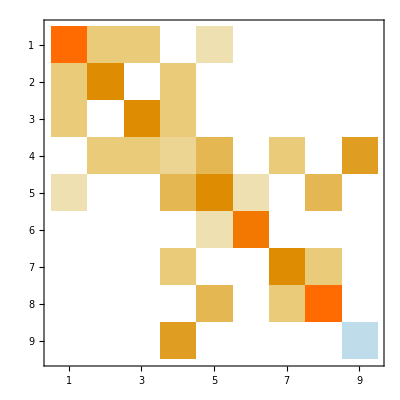

```mathematica
hEvenPMatrix//MatrixPlot
```

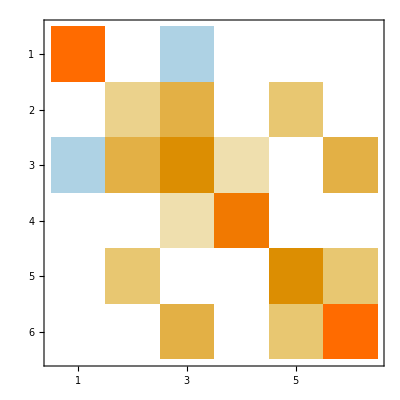

```mathematica
hOddPMatrix//MatrixPlot
```

## Diagonalize the Hamiltonian

### Get eigen energies in both parity sectors

```mathematica
(* esystem = Normal@hMatrix//Eigensystem; *)
(* evalues=esystem[[1]]//Re; *)
```

```mathematica
esystemEvenP = Normal@hEvenPMatrix//Eigensystem ;
```

```mathematica
evaluesEvenP=esystemEvenP[[1]]//Re
```

{4.00385,3.2341,2.45323,2.17946,-1.68011,1.667,1.50785,1.07845,0.225166}

```mathematica
esystemOddP = Normal@hOddPMatrix//Eigensystem;
```

```mathematica
evaluesOddP=esystemOddP[[1]]//Re
```

{3.77994,2.74861,2.42191,1.667,1.43078,-0.379246}

For each eigenvector, stores coefficients of the expansion of the eigenvector in the basis specified above

```mathematica
evectorsEvenP= esystemEvenP[[2]];
evectorsOddP= esystemOddP[[2]];
(* get the eigenvectors *)
evectorKetsEvenP = Simplify[evenPSector.evectorsEvenP];
evectorKetsOddP = Simplify[oddPSector.evectorsOddP];
```

```mathematica
E0EvenP = evaluesEvenP// Sort //First;
```

```mathematica
E0OddP = evaluesOddP // Sort // First;
```

```mathematica
E0=Min[E0EvenP, E0OddP]
```

-1.68011

```mathematica
evaluesEvenPShifted = (evaluesEvenP - E0) // Sort 
evaluesOddPShifted = (evaluesOddP - E0) // Sort 
(* excited levels agree, but eigenvectors are not yet separated into parity / momentum sectors *)
```

{0.,1.90528,2.75856,3.18797,3.34711,3.85957,4.13335,4.91421,5.68397}

{1.30087,3.1109,3.34711,4.10202,4.42872,5.46006}

## Make a plot for the Low-Lying Energy Spectrum

```mathematica
emax = 3.5; (* map energies below max value *)
eTickStep = 0.5; (* spacing of ticks between zero and eMax *)
eLowerPadding = 0.1; (* padding between emin and lower plot range for the y-axis *)
(* the plot of the energy spectrum will be like a stacked bar chart *)
barWidth = 1.0; (* the width of bars for either parity value *)
barPadding = 0.3; (* spacing between the two bar stacks *)
(* leftmost and rightmost point on the x-axis for the two bar stacks  *)
evenBoundL = 0.7; 
evenBoundR = evenBoundL + barWidth;
oddBoundL = evenBoundR + barPadding;
oddBoundR = oddBoundL + barWidth;
(* plot ticks on the x-axis label the two stacks *)
evenTick = 0.5(evenBoundL + evenBoundR);
oddTick = 0.5(oddBoundL + oddBoundR);
(* define y-axis ticks for the eigenenergies *)
energyTicks = Table[en, {en, 0, emax, eTickStep}];
(* padding to determine the x-range of the plot *)
paddingL = 0.7;
paddingR = 2.0;
plotRangeL = evenBoundL - paddingL;
plotRangeR = oddBoundR + paddingR;
```

```mathematica
(* compute energy differences for the stacked bar chart *)
```

```mathematica
energies = Table[Select[list, # < emax &], 
{list,{evaluesEvenPShifted, evaluesOddPShifted}}]
```

{{0.,1.90528,2.75856,3.18797,3.34711},{1.30087,3.1109,3.34711}}

```mathematica
plot1 =ListLinePlot[Table[{{evenBoundL, en}, {evenBoundR, en}}, {en, energies[[1]]}], PlotStyle->Red];
plot2=ListLinePlot[Table[{{oddBoundL, en}, {oddBoundR, en}}, {en, energies[[2]]}], PlotStyle->Blue];
```

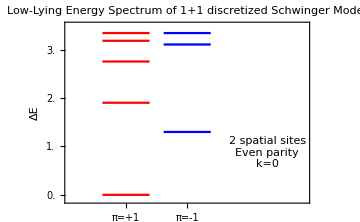

```mathematica
savagePlot = Show[
plot1, (* stacked bars for π=+1 parity eigenenergies *)
plot2, (* stacked bars for π=-1 parity eigenenergies *) 
PlotRange -> {{plotRangeL, plotRangeR},{0.0 - eLowerPadding, emax}},
AxesOrigin-> {plotRangeL, 0},
PlotLabel->Style["Low-Lying Energy Spectrum of\n1+1 discretized Schwinger Model", Black, FontSize->15],
Epilog->Style[Text["2 spatial sites\nEven parity\nk=0",{oddBoundR + 0.6(plotRangeR - oddBoundR),emax / 4.}],15],
Frame->True,
FrameLabel->{None,Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicks->{{energyTicks, None}, {{{evenTick, "π=+1"}, {oddTick,"π=-1"}}, {None, None}}},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 20]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
```

## Get the eigenstate ket expansion

### Coefficients for the ground state

```mathematica
gsCoeffs = evectorsEvenP[[ Position[evaluesEvenP, E0][[1, 1]] ]] //Chop//Rationalize
```

{-0.0757819,0.151499,0.151499,-0.641343,0.230437,-0.0287069,0.151906,-0.0777094,0.67379}

```mathematica
evaluesEvenPSorted = evaluesEvenP// Sort
evaluesOddPSorted =evaluesOddP // Sort
```

{-1.68011,0.225166,1.07845,1.50785,1.667,2.17946,2.45323,3.2341,4.00385}

{-0.379246,1.43078,1.667,2.42191,2.74861,3.77994}

### Coefficients for the states in either parity sector

```mathematica
eEvenPCoeffs=Table[
(* find the index of the ith even-parity excited state in the array of the corresponding eigenvectors; each array element is a list of coefficients for the expansion of that eigenvector in terms of the original basis *)
evectorsEvenP⟦Position[evaluesEvenP, evaluesEvenPSorted⟦i⟧]⟦1, 1⟧ ⟧ //Chop//Rationalize,
(* note that the first element is the ground state *)
{i, 2, Length[evaluesEvenPSorted]}];
eOddPCoeffs=Table[
(* find the index of the ith even-parity excited state in the array of the corresponding eigenvectors; each array element is a list of coefficients for the expansion of that eigenvector in terms of the original basis *)
evectorsOddP⟦Position[evaluesOddP, evaluesOddPSorted⟦i⟧]⟦1, 1⟧ ⟧ //Chop//Rationalize,
{i, Length[evaluesOddPSorted]}];
```

### Corresponding expansions

```mathematica
gsExpans= Expand[gsCoeffs.evenPSector];
eEvenPExpans = Table[Expand[eEvenPCoeffs⟦i⟧.evenPSector], {i, Length[eEvenPCoeffs]}];
eOddPExpans = Table[Expand[eOddPCoeffs⟦i⟧.oddPSector], {i, Length[eOddPCoeffs]}];
es1Expans = Expand[e1Coeffs.oddPSector];
es2Expans = Expand[e2Coeffs.evenPSector];
```

## Convert spins to Fermions

Define an operator to convert spins to fermions

```mathematica
spinMap = {
(* sends the ket of spins + links to a ket of fermions + links *)
		
S.psi_Ket:> Ket @@ (* apply ket again *)
(Flatten[(Partition[List[ (* parition the list into a list of spins and a list of kets*)
(* delete the ket head to split the list into spins and kets *)
Delete[0]@psi], 
	(* spins are converted to fermions, links are untouched *)
nfs]+{1, 0})*{1/2,1}]) ,
S.(x_ psi_Ket):>x S.psi/;NumericQ[x]};
```

```mathematica
rules =Join[basics,normalization, translation, parity, operators, spinMap];
```

Converted expansion

### π = +1

#### Ground State

Dominated by 
	the strong-coupling limit antiferromagnetic state,  
	a linear combination of all states where one fermion hopped, and 
	a linear combination of all states where hopping two fermions hopped in the same direction

```mathematica
gsTable =Reverse@SortBy[Table[
{gsCoeffs[[i]],
(* print the result of Hmass acting on the ket *)
N[(1/(m *nfs)) * Hmass/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.evenPSector[[i]]//. rules}, {i, Length[evenPSector]}]
,Abs[First[#]] &];
gsTableForm = TableForm[gsTable,
TableHeadings->{Table[j, {j, 1, Length[evenPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | 0.67379 | -0.5 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
2 | -0.641343 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
3 | 0.230437 | 0. | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
4 | 0.151906 | 0. | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
5 | 0.151499 | 0. | 2. | 1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)
6 | 0.151499 | 0. | 2. | 1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)
7 | -0.0777094 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)
8 | -0.0757819 | 0.25 | 3. | (0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
9 | -0.0287069 | -0.25 | 3. | (0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)

```mathematica
(*Export[StringJoin["~/Desktop/gsTable_NFS_",ToString[nfs], "_L1_", ToString[Λ1],"_L2_",ToString[Λ2],".png"],
gsTableForm, 
ImageResolution->imageRes]*)
```

#### 1st even-parity excited state

Compared to the ground state, 
	there is less overlap onto the strong-coupling limit antiferromagnetic state,
	for nfs = 4, higher-winding number states also becomes important (as seen by larger charge on the links)

```mathematica
e1EvenTable =Reverse@SortBy[Table[
{eEvenPCoeffs⟦1⟧⟦i⟧,
(* print the result of Hmass acting on the ket *)
N[(1/(m *nfs)) * Hmass/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.evenPSector[[i]]//. rules}, {i, Length[evenPSector]}],
Abs[First[#]] &];
e1EveneTableForm = TableForm[e1EvenTable,
TableHeadings->{Table[j, {j, 1, Length[evenPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | 0.625506 | -0.5 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
2 | -0.479718 | 0. | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
3 | 0.269849 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)
4 | -0.253631 | 0. | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
5 | 0.247319 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
6 | -0.23666 | 0. | 2. | 1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)
7 | -0.23666 | 0. | 2. | 1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)
8 | 0.235245 | 0.25 | 3. | (0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
9 | 0.113767 | -0.25 | 3. | (0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)

```mathematica
(*Export[StringJoin["~/Desktop/e2Table_NFS_",ToString[nfs], "_L1_", ToString[Λ1],"_L2_",ToString[Λ2],".png"],
 e2TableForm, 
ImageResolution->imageRes]*)
```

#### 2nd even-parity excited state

Compared to the 2nd excited state, 
	there is very little overlap onto the strong-coupling limit antiferromagnetic state,
	the superposition of states where both fermions hopped in the same direction becomes important, and 
	higher-winding number state also becomes important (as seen by larger charge on the links)

```mathematica
e2EvenTable =Reverse@SortBy[Table[
{eEvenPCoeffs⟦2⟧⟦i⟧,
(* print the result of Hmass acting on the ket *)
N[(1/(m *nfs)) * Hmass/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.evenPSector[[i]]//. rules}, {i, Length[evenPSector]}],
 Abs[First[#]] &];
e2EvenTableForm = TableForm[e2EvenTable,
TableHeadings->{Table[j, {j, 1, Length[evenPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | -0.484674 | 0. | 2. | 1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)
2 | -0.484674 | 0. | 2. | 1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)
3 | -0.379325 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)
4 | 0.356815 | 0. | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
5 | 0.350459 | 0. | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
6 | 0.321074 | 0.25 | 3. | (0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
7 | -0.13962 | -0.25 | 3. | (0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
8 | 0.0824381 | -0.5 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
9 | 0.0823354 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)

```mathematica
(*Export[StringJoin["~/Desktop/e4Table_NFS_",ToString[nfs], "_L1_", ToString[Λ1],"_L2_",ToString[Λ2],".png"],
 e2EvenTable, 
ImageResolution->imageRes]*)
```

#### 3rd even-parity excited state

```mathematica
e3EvenTable =Reverse@SortBy[Table[
{eEvenPCoeffs⟦3⟧⟦i⟧,
(* print the result of Hmass acting on the ket *)
N[(1/(m *nfs)) * Hmass/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->evenPSector⟦i⟧/.params//.rules].evenPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.evenPSector[[i]]//. rules}, {i, Length[evenPSector]}],
Abs[First[#]] &];
e3EvenTableForm = TableForm[e3EvenTable,
TableHeadings->{Table[j, {j, 1, Length[evenPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | 0.722751 | 0. | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
2 | -0.534232 | 0. | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
3 | 0.323523 | -0.25 | 3. | (0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
4 | -0.182647 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
5 | 0.171852 | 0.25 | 3. | (0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
6 | -0.14024 | -0.5 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
7 | 0.0479617 | 0. | 2. | 1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)
8 | 0.0479617 | 0. | 2. | 1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)
9 | 0.0199798 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)

### π = -1

#### 1st odd-parity excited state

The odd-parity first excited state is dominated by 
	a linear combination of states where one fermion hopped, with alternating overall sign depending on the direction of hopping; and
	a superposition of states where both fermions hopped, again with the overall sign as expected

```mathematica
e1OddTable =Reverse@SortBy[Table[
{eOddPCoeffs⟦1⟧⟦i⟧,
(* print the result of Hmass acting on the ket *)
N[(1/(m *nfs)) * Hmass/.Ket[Ψ]->oddPSector⟦i⟧/.params//.rules].oddPSector⟦i⟧//.rules,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->oddPSector⟦i⟧/.params//.rules].oddPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.oddPSector[[i]]//. rules}, {i, Length[oddPSector]}],
Abs[First[#]] &];
e1OddTableForm = TableForm[e1OddTable,
TableHeadings->{Table[j, {j, 1, Length[oddPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | -0.729429 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
2 | 0.523384 | 0. | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0-0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0-1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
3 | 0.33858 | 0. | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
4 | -0.250364 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)
5 | -0.0964677 | -0.25 | 3. | (-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
6 | 0.0858924 | 0.25 | 3. | (-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)

```mathematica
(*Export[StringJoin["~/Desktop/e1Table_NFS_",ToString[nfs], "_L1_", ToString[Λ1],"_L2_",ToString[Λ2],".png"],
e1OddTableForm, 
ImageResolution->imageRes]*)
```

#### 2nd odd-parity excited state

Compared to the fist excited state, the third excited state has a larger contribution from the states with higher winding numbers

```mathematica
e2OddTable =Reverse@SortBy[Table[
{eOddPCoeffs⟦2⟧⟦i⟧,
(* print the result of Hmass acting on the ket *)
N[(1/(m *nfs)) * Hmass/.Ket[Ψ]->oddPSector⟦i⟧/.params//.rules].oddPSector⟦i⟧//.rules,
(* print the result of Hfield acting on the ket *)
N[(1/J) * Hfield/.Ket[Ψ]->oddPSector⟦i⟧/.params//.rules].oddPSector⟦i⟧//.rules,
(* print the actual ket expansion converted to fermionic sites *)
S.oddPSector[[i]]//. rules}, {i, Length[oddPSector]}],
 Abs[First[#]] &];
e2OddTableForm = TableForm[e2OddTable,
TableHeadings->{Table[j, {j, 1, Length[oddPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | -0.625318 | 0. | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0-0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0-1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
2 | 0.454623 | 0. | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
3 | -0.397564 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
4 | 0.346353 | -0.25 | 3. | (-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
5 | -0.252813 | 0.25 | 3. | (-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
6 | 0.245691 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)

```mathematica
(*Export[StringJoin["~/Desktop/e3Table_NFS_",ToString[nfs], "_L1_", ToString[Λ1],"_L2_",ToString[Λ2],".png"],
 e2OddTable, 
ImageResolution->imageRes]*)
```

## Define interpolating operators

Define effective mass and basic operators

```mathematica
ClearAll[g]
g[ovrlapSrc_,ovrlapSnk_, energies_,t_, T_]:=Total[Table[Abs[ovrlapSrc⟦i⟧ *ovrlapSnk⟦i⟧]/(2 (energies⟦i⟧ -energies⟦1⟧)) *
( Exp[-(energies⟦i⟧ -energies⟦1⟧)*t]+ Exp[-(energies⟦i⟧ -energies⟦1⟧)*(T - t)]) ,
{i, 2, Length[energies]}]];
```

```mathematica
density ={
SubPlus[χ][i_].psi_Ket :>If[psi[[i + 1]] == 1,0,ReplacePart[psi, i + 1->psi[[i+ 1]] + 1]],
SubPlus[χ][i_].(x_ psi_Ket):>x SubPlus[χ][i].psi/;NumericQ[x],
SubMinus[χ][i_].psi_Ket :>If[psi[[i + 1]] == 0,0,ReplacePart[psi, i+ 1->psi[[i + 1]]-1]],
SubMinus[χ][i_].(x_ psi_Ket):>x SubMinus[χ][i].psi/;NumericQ[x]};
```

```mathematica
rules =Join[basics,normalization, translation, parity, operators, spinMap, density];
```

Define naive interpolating operators

#### Chiral density

```mathematica
χ0Src= (-1)^1 SubPlus[χ][1].SubMinus[χ][1].state ;
χ0Snk= 2/nfs Sum[(-1)^i SubPlus[χ][i].SubMinus[χ][i].state , {i, 1, nfs-1, 2}];
```

#### “Hopping Density”

Good projection on π = -1

```mathematica
M01Src =SubPlus[χ][fs[0]].SubPlus[U][fs[0]].SubMinus[χ][fs[1]].state -SubPlus[χ][fs[2]].SubMinus[U][fs[1]].SubMinus[χ][fs[1]].state ;
M01Snk =2/nfs Sum[SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state -SubPlus[χ][fs[i]].SubPlus[U][fs[i+1]].SubMinus[χ][fs[i+1]].state, 
{i, 1, nfs-1, 2}];
```

Bad projection on π = -1 (original bug)

```mathematica
M01SrcBad =SubPlus[χ][fs[0]].SubPlus[U][fs[0]].SubMinus[χ][fs[1]].state -SubPlus[χ][fs[1]].SubMinus[U][fs[0]].SubMinus[χ][fs[0]].state ;
M01SnkBad =2/nfs Sum[SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state -SubPlus[χ][fs[i-1]].SubPlus[U][fs[i-1]].SubMinus[χ][fs[i]].state, 
{i, 1, nfs-1, 2}];
```

#### Get the parity eigenstate expansion in terms of fermions (not spins)

```mathematica
(* expansion of energy eigenstates in terms of the even- and odd- parity states, converted to fermionic description *)
```

```mathematica
gs = Table[gsCoeffs⟦i⟧ * S.evenPSector[[i]]//. rules, {i, Length[evenPSector]}];
eOddP = Table[
Table[eOddPCoeffs⟦j⟧⟦i⟧ * S.oddPSector[[i]]//. rules, {i, Length[oddPSector]}],
{j, 1, Length[eOddPCoeffs]}];
eEvenP = Table[
Table[eEvenPCoeffs⟦j⟧⟦i⟧ * S.evenPSector[[i]]//. rules, {i, Length[evenPSector]}],
{j, 1, Length[eEvenPCoeffs]}];
```

```mathematica
(* list of all eigen energies: first all even-parity, then all odd-parity *)
energiesParitySorted = Join[Sort[evaluesEvenP], Sort[evaluesOddP]];
```

```mathematica
(* expansion of even- and odd- parity states in terms of the original basis converted to fermionic description *)
```

```mathematica
evenPSectorF = Table[S.evenPSector[[i]]//. rules, {i, Length[evenPSector]}];
oddPSectorF = Table[S.oddPSector[[i]]//. rules, {i, Length[oddPSector]}];
```

```mathematica
χ0SrcOnGS =Table[Expand[χ0Src/.state->basisKet//.rules],{basisKet,gs}];
χ0SnkOnGS =Table[Expand[χ0Snk/.state->basisKet//.rules],{basisKet,gs}];
M01SrcOnGS = Table[Expand[M01Src/.state->basisKet//.rules],{basisKet,gs}];
M01SnkOnGS = Table[Expand[M01Snk/.state->basisKet//.rules],{basisKet,gs}];
M01SrcBadOnGS = Table[Expand[M01SrcBad/.state->basisKet//.rules],{basisKet,gs}];
M01SnkBadOnGS = Table[Expand[M01SnkBad/.state->basisKet//.rules],{basisKet,gs}];
```

Construct an operator that takes GS to E1

```mathematica
bareVac =Ket@@Join[Table[Boole[Mod[i, 2] == 0], {i,1, nfs}], ConstantArray[0, nfs]]
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

## Construct an operator for BareVac ⇒ π = +1 state

### Inspect GS expansion

```mathematica
TableForm[gsTable,
TableHeadings->{Table[j, {j, 1, Length[evenPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | 0.67379 | -0.5 | 0 | 0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0
2 | -0.641343 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
3 | 0.230437 | 0. | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
4 | 0.151906 | 0. | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
5 | 0.151499 | 0. | 2. | 1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)
6 | 0.151499 | 0. | 2. | 1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)
7 | -0.0777094 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)
8 | -0.0757819 | 0.25 | 3. | (0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)
9 | -0.0287069 | -0.25 | 3. | (0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)

```mathematica
gsExpanded = Expand[Simplify[Total[gs]]];
```

### Create operators for hopping into each π=+1 state

#### 8th π=+1 state

#### Definition

```mathematica
(* simultaneous hopping on two neighboring even sites away from each other, summed over all even sites *)
```

```mathematica
gsOp[8]=1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state 
+ SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state
+ SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+6]].SubMinus[U][fs[i+5]].SubMinus[χ][fs[i+5]].state), 
{i, 0, nfs-1, 2}];
gsOpDag[8]=1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state 
+ SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state
+ SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+6]].SubMinus[U][fs[i+5]].SubMinus[χ][fs[i+5]].state), 
{i, 1, nfs, 2}];
```

#### Check

```mathematica
gsTable⟦8,4⟧
```

1/(2 √2)(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)

```mathematica
gsOp[8]/.state->bareVac//.rules
```

1/(2 √2)(0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0+1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0+1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1+1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)

```mathematica
gsOpDag[8]/.state->gsTable⟦8, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 5th π=+1 state

#### Definition

```mathematica
(* 
simultaneous hopping on two even sites toward each other, separated by three sites,summed over all even sites 
*)
```

```mathematica
gsOp[5]=1/2 Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].state), 
{i, 0, nfs-1, 2}];
gsOpDag[5]=1/2 Sum[( SubPlus[χ][fs[i-1]].SubPlus[U][fs[i-1]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i+3]].SubMinus[U][fs[i+2]].SubMinus[χ][fs[i+2]].state), 
{i, 0, nfs-1, 2}];
```

#### Check

```mathematica
gsTable⟦5, 4⟧
```

1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)

```mathematica
gsOp[5]/.state->bareVac//.rules
```

1/2 (0,0,1,1,1,0,0,1,0,-1,0,0,1,0,0,0+0,1,0,0,1,1,1,0,0,0,0,-1,0,0,1,0+1,0,0,1,0,0,1,1,1,0,0,0,0,-1,0,0+1,1,1,0,0,1,0,0,0,0,1,0,0,0,0,-1)

```mathematica
gsOpDag[5]/.state->gsTable⟦5, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 6th π=+1 state

#### Definition

```mathematica
(* 
simultaneous hopping on two neighboring even sites away from each other, summed over all even sites 
*)
```

```mathematica
gsOp[6]=1/2 Sum[( SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state), 
{i, 0, nfs-1, 2}];
gsOpDag[6]=1/2 Sum[( SubPlus[χ][fs[i+1]].SubMinus[U][fs[i]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i+3]].SubPlus[U][fs[i+3]].SubMinus[χ][fs[i+4]].state), 
{i, 0, nfs-1, 2}];
```

#### Check

```mathematica
gsTable⟦6, 4⟧
```

1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)

```mathematica
gsOp[6]/.state->bareVac//.rules
```

1/2 (0,0,1,1,0,1,1,0,0,-1,0,0,0,0,1,0+0,1,1,0,0,0,1,1,0,0,1,0,0,-1,0,0+1,0,0,0,1,1,0,1,1,0,0,-1,0,0,0,0+1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,-1)

```mathematica
gsOpDag[6]/.state->gsTable⟦6, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 2nd π=+1 state

#### Definition

```mathematica
(* hopping from even sites to odd site, summed over all even sites *)
```

```mathematica
gsOp[2]=1/(2 √2)Sum[SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state +SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state, 
{i, 0, nfs-1, 2}];
gsOpDag[2] =1/(2 √2)Sum[SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state +SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state, 
{i, 1, nfs, 2}];
```

#### Check

```mathematica
gsTable⟦2, 4⟧
```

1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)

```mathematica
gsOp[2]/.state->bareVac//.rules
```

1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0+0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0+0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0+0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0+1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)

```mathematica
gsOpDag[2]/.state->gsTable⟦2, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 3rd π=+1 state

#### Definition

```mathematica
(* simultaneous hopping on two neighboring even sites in the same direction, summed over all even sites *)
```

```mathematica
gsOp[3]=1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].state 
+ SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state), 
{i, 0, nfs-1, 2}];
gsOpDag[3]=1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].state 
+ SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state), 
{i, 1, nfs, 2}];
```

#### Check

```mathematica
gsTable⟦3,4⟧
```

1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)

```mathematica
gsOp[3]/.state->bareVac//.rules
```

1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0+0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0+0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0+1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0+1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)

```mathematica
gsOpDag[3]/.state->gsTable⟦3, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### *** 9th π=+1 state ***

#### Definition

```mathematica
(* 

SMALL WEIGHT. This particular state would be hard to realize in Monte-Carlo.

simultaneous hopping of on two neighboring even sites in the same direction; on of the fermions jumps twice so they end on neighboring (fermionic) sites; summed over all even sites 

*)
```

```mathematica
gsOp[9]=1/(2 √2)Sum[( SubPlus[χ][fs[i+1]].SubMinus[U][fs[i]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].state 
+ SubPlus[χ][fs[i-1]].SubPlus[U][fs[i-1]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].state ), 
{i, 0, nfs-1, 2}];
gsOpDag[9]=1/(2 √2)Sum[(SubPlus[χ][fs[i+1]].SubPlus[U][fs[i+1]].SubMinus[χ][fs[i+2]]. SubPlus[χ][fs[i-1]].SubPlus[U][fs[i-1]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state 
+ SubPlus[χ][fs[i-1]].SubMinus[U][fs[i-2]].SubMinus[χ][fs[i-2]].SubPlus[χ][fs[i+1]].SubMinus[U][fs[i]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state ), 
{i, 0, nfs-1, 2}];
```

#### Check

```mathematica
gsTable⟦9,4⟧
```

1/(2 √2)(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
gsOp[9]/.state->bareVac//.rules
```

1/(2 √2)(0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0+0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0+0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1+1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
gsOpDag[9]/.state->gsTable⟦9, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 4th π=+1 state

#### Definition

```mathematica
(* 
simultaneous hopping on two even sites in the same direction, separated by three sites, summed over all even sites 
*)
```

```mathematica
gsOp[4]=1/2 Sum[(SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state 
+SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state), 
{i, 0, nfs-5, 2}];
gsOpDag[4]=1/2 Sum[(SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state 
+SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state), 
{i, 1, nfs-4, 2}];
```

#### Check

```mathematica
gsTable⟦4, 4⟧
```

1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)

```mathematica
gsOp[4]/.state->bareVac//.rules
```

1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0+0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0+1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)

```mathematica
gsOpDag[4]/.state->gsTable⟦4, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 7th π=+1 state

#### Definition

```mathematica
(* 
simultaneous hopping on three neighboring even sites in the same direction, summed over all even sites 
*)
```

```mathematica
gsOp[7]=1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state 
+ SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].state), 
{i, 0, nfs-1, 2}];
gsOpDag[7]=1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state 
+ SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].state), 
{i, 1, nfs, 2}];
```

#### Check

```mathematica
gsTable⟦7,4⟧
```

1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
gsOp[7]/.state->bareVac//.rules
```

1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0+0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0+1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0+1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0+1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
gsOpDag[7]/.state->gsTable⟦7, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 1st π=+1 state

```mathematica
(* ground state stays in the ground state*)
```

```mathematica
gsOp[1] =state;
gsOpDag[1] =state;
```

### Construct the full operator

```mathematica
Block[{ntrunc, norm},
ntrunc = Length[Select[gsTable, #⟦3⟧ ≤ Λ3 &] ];(* TRUNCATE THE SMART OPERATOR *)
norm=Sqrt[Sum[gsTable⟦i, 1⟧^2, {i, 1, Min[ntrunc, 9]}]]; (* RENORMALIZE THE COEFFICIENTS *)
bareToGS= (1/norm) Sum[gsTable⟦i, 1⟧ gsOp[i], {i, 1, Min[ntrunc, 9]}]];
```

```mathematica
BareToGSState=(Expand[bareToGS/.state-> bareVac //.rules]);
```

```mathematica
(* check overlap onto ground state *)
((Expand[bareToGS/.state-> bareVac //.rules]).(gsExpanded))//.rules
```

1.

## Construct an operator for π = +1 state ⇒ BareVac

### Set up basic rules

```mathematica
(* 
Ideally this operator should be defined as the inverse of the operator for 
BareVac => π=+1 state.
This is "cheating".
I trust there is a legitimate way to do this on a quantum computer: given a series of gates, to run their inverses in the opposite order. 
*)
```

```mathematica
killsGS = {
(* kills the ket if the link is not zero *)	
δl[i_].psi_Ket:> If[psi⟦nfs+1 + i⟧ ==0, psi,0],
δl[i_].(x_ psi_Ket):>x δl[i].psi/;NumericQ[x]};
```

```mathematica
rules =Join[basics,normalization, translation, parity, operators, spinMap, density, killsGS];
```

### Define the operator

```mathematica
GSToBare= 1/gsTable⟦1, 1⟧Apply[Dot,Table[δl[i], {i, 0, nfs-1}]].state;
GSStateToBare=(Expand[GSToBare/.state-> gsExpanded //.rules]);
```

```mathematica
(* check overlap onto ground state *)
((Expand[GSToBare/.state-> gsExpanded //.rules]).(bareVac))//.rules
```

1.

## Construct an operator for BareVac ⇒ π = -1 state

### Inspect E1 expansion

```mathematica
TableForm[e1OddTable,
TableHeadings->{Table[j, {j, 1, Length[oddPSector]}],{"weight", "mass", "charge", "state"}}]
```

| weight | mass | charge | state
1 | -0.729429 | -0.25 | 1. | (0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)/(2 √2)
2 | 0.523384 | 0. | 2. | (0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0-0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0-1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)/(2 √2)
3 | 0.33858 | 0. | 2. | 1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)
4 | -0.250364 | 0.25 | 3. | (0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)/(2 √2)
5 | -0.0964677 | -0.25 | 3. | (-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)/(2 √2)
6 | 0.0858924 | 0.25 | 3. | (-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)/(2 √2)

```mathematica
e1Expanded = Expand[Simplify[Total[eOddP⟦1⟧]]];
```

### Create operators for hopping into each π=-1 eigenstate

#### 6th π=-1 state

#### Definition

```mathematica
(* 
	simultaneous hopping on two neighboring even sites in the same direction and in the opposite direction on the even site after the following one, summed over all even sites

two jumps to the right => minus sign; two jumps to the left => plus sign
*)
```

```mathematica
e1Op[6]=1/(2 √2)Sum[( -SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state 
+ SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state
+ SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+6]].SubMinus[U][fs[i+5]].SubMinus[χ][fs[i+5]].state), 
{i, 0, nfs-1, 2}];
e1OpDag[6]=-1/(2 √2)Sum[(- SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state 
+ SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state
+ SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+6]].SubMinus[U][fs[i+5]].SubMinus[χ][fs[i+5]].state), 
{i, 1, nfs, 2}];
```

#### Check

```mathematica
e1OddTable⟦6, 4⟧
```

1/(2 √2)(-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)

```mathematica
e1Op[6]/.state->bareVac//.rules
```

1/(2 √2)(-0,0,1,0,1,1,1,0,0,-1,0,-1,0,0,1,0+0,0,1,1,1,0,1,0,0,-1,0,0,1,0,1,0-1,0,0,0,1,0,1,1,1,0,0,-1,0,-1,0,0+1,0,0,0,1,1,1,0,1,0,0,-1,0,0,1,0+1,0,1,0,0,0,1,1,1,0,1,0,0,-1,0,0-1,0,1,1,1,0,0,0,0,-1,0,0,1,0,0,-1-1,1,1,0,0,0,1,0,0,0,1,0,0,-1,0,-1+1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,-1)

```mathematica
e1OpDag[6]/.state->e1OddTable⟦6, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 1st π=-1 state

#### Definition

```mathematica
(* 
hopping from even sites to odd site, summed over all even sites,hopping to the right => plus sign, hopping to the left => minus sign
 *)
```

```mathematica
e1Op[1]=1/(2 √2)Sum[-SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state +SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state, 
{i, 0, nfs-1, 2}];
e1OpDag[1] =-1/(2 √2)Sum[-SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state +SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state, 
{i, 1, nfs, 2}];
```

#### Check

```mathematica
e1OddTable⟦1, 4⟧
```

1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)

```mathematica
e1Op[1]/.state->bareVac//.rules
```

1/(2 √2)(0,0,1,1,0,1,0,1,0,-1,0,0,0,0,0,0+0,1,0,0,1,1,0,1,0,0,0,-1,0,0,0,0+0,1,0,1,0,0,1,1,0,0,0,0,0,-1,0,0-0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0-0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0-0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0-1,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0+1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,-1)

```mathematica
e1OpDag[1]/.state->e1OddTable⟦1, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 2nd π=-1 state

#### Definition

```mathematica
(* 
simultaneous hopping on two neighboring even sites in the same direction, summed over all even sites, 
jumps to the right => plus sign; jumps to the left => minus sign
*)
```

```mathematica
e1Op[2]=1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].state 
- SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state), 
{i, 0, nfs-1, 2}];
e1OpDag[2]=-1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].state 
- SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state), 
{i, 1, nfs, 2}];
```

#### Check

```mathematica
e1OddTable⟦2, 4⟧
```

1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0-0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0-1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)

```mathematica
e1Op[2]/.state->bareVac//.rules
```

1/(2 √2)(0,0,1,0,1,1,0,1,0,-1,0,-1,0,0,0,0+0,1,0,0,1,0,1,1,0,0,0,-1,0,-1,0,0-0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0-0,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0-1,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0-1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0+1,0,1,1,0,1,0,0,0,-1,0,0,0,0,0,-1+1,1,0,1,0,0,1,0,0,0,0,0,0,-1,0,-1)

```mathematica
e1OpDag[2]/.state->e1OddTable⟦2, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 5th π=-1 state

#### Definition

```mathematica
(* 

SMALL WEIGHT. This particular state would be hard to realize in Monte-Carlo.

simultaneous hopping of on two neighboring even sites in the same direction; on of the fermions jumps twice so they end on neighboring (fermionic) sites; summed over all even sites 

Jumps to the right => plus sign; Jumps to the left => minus sign
*)
```

```mathematica
e1Op[5]=1/(2 √2)Sum[( SubPlus[χ][fs[i+1]].SubMinus[U][fs[i]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].state 
- SubPlus[χ][fs[i-1]].SubPlus[U][fs[i-1]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].state ), 
{i, 0, nfs-1, 2}];
e1OpDag[5]=1/(2 √2)Sum[(SubPlus[χ][fs[i+1]].SubPlus[U][fs[i+1]].SubMinus[χ][fs[i+2]]. SubPlus[χ][fs[i-1]].SubPlus[U][fs[i-1]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].state 
- SubPlus[χ][fs[i-1]].SubMinus[U][fs[i-2]].SubMinus[χ][fs[i-2]].SubPlus[χ][fs[i+1]].SubMinus[U][fs[i]].SubMinus[χ][fs[i]].SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].state ), 
{i, 0, nfs-1, 2}];
```

#### Check

```mathematica
e1OddTable⟦5, 4⟧
```

1/(2 √2)(-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
e1Op[5]/.state->bareVac//.rules
```

1/(2 √2)(-0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1+0,0,0,1,1,1,0,1,0,-1,-1,-1,0,0,0,0+0,1,0,0,0,1,1,1,0,0,0,-1,-1,-1,0,0-0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0-0,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0+0,1,1,1,0,1,0,0,-1,-1,0,0,0,0,0,-1-1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0+1,1,0,1,0,0,0,1,0,0,0,0,0,-1,-1,-1)

```mathematica
e1OpDag[5]/.state->e1OddTable⟦5, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 3rd π=-1 state

#### Definition

```mathematica
(* 
simultaneous hopping on two even sites in the same direction, separated by three sites, summed over all even sites,
jumps to the right => plus sign; jumps to the left => minus sign
*)
```

```mathematica
e1Op[3]=1/2 Sum[(- SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state 
+SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state), 
{i, 0, nfs-5, 2}];
e1OpDag[3]=-1/2 Sum[(-SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubPlus[U][fs[i+4]].SubMinus[χ][fs[i+5]].state 
+SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state), 
{i, 1, nfs-4, 2}];
```

#### Check

```mathematica
e1OddTable⟦3, 4⟧
```

1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)

```mathematica
e1Op[3]/.state->bareVac//.rules
```

1/2 (0,0,1,1,0,0,1,1,0,-1,0,0,0,-1,0,0-0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,0-1,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0+1,1,0,0,1,1,0,0,0,0,0,-1,0,0,0,-1)

```mathematica
e1OpDag[3]/.state->e1OddTable⟦3, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

#### 4th π=-1 state

#### Definition

```mathematica
(* 
simultaneous hopping on three neighboring even sites in the same direction, summed over all even sites, 
jumps to the right => plus sign,
jumps to the left => minus sign
*)
```

```mathematica
e1Op[4]=1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state 
- SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].state), 
{i, 0, nfs-1, 2}];
e1OpDag[4]=-1/(2 √2)Sum[( SubPlus[χ][fs[i]].SubMinus[U][fs[i-1]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i+2]].SubMinus[U][fs[i+1]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+4]].SubMinus[U][fs[i+3]].SubMinus[χ][fs[i+3]].state 
- SubPlus[χ][fs[i-2]].SubPlus[U][fs[i-2]].SubMinus[χ][fs[i-1]].SubPlus[χ][fs[i]].SubPlus[U][fs[i]].SubMinus[χ][fs[i+1]].SubPlus[χ][fs[i+2]].SubPlus[U][fs[i+2]].SubMinus[χ][fs[i+3]].state), 
{i, 1, nfs, 2}];
```

#### Check

```mathematica
e1OddTable⟦4, 4⟧
```

1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
e1Op[4]/.state->bareVac//.rules
```

1/(2 √2)(0,0,1,0,1,0,1,1,0,-1,0,-1,0,-1,0,0-0,1,1,0,1,0,1,0,0,0,1,0,1,0,1,0-1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,0-1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0-1,0,1,0,1,0,0,1,1,0,1,0,1,0,0,0+1,0,1,0,1,1,0,0,0,-1,0,-1,0,0,0,-1+1,0,1,1,0,0,1,0,0,-1,0,0,0,-1,0,-1+1,1,0,0,1,0,1,0,0,0,0,-1,0,-1,0,-1)

```mathematica
e1OpDag[4]/.state->e1OddTable⟦4, 4⟧//.rules
```

0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0

### Construct the full operator

```mathematica
Block[{ntrunc, norm},
ntrunc = Length[Select[e1OddTable, #⟦3⟧ ≤ Λ3 &] ];(* TRUNCATE THE SMART OPERATOR *)
norm=Sqrt[Sum[e1OddTable⟦i, 1⟧^2, {i, 1, Min[ntrunc, 6]}]]; (* RENORMALIZE THE COEFFICIENTS *)
bareToE1= (1/norm) Sum[e1OddTable⟦i, 1⟧ e1Op[i], {i, 1, Min[ntrunc, 6]}]];
```

```mathematica
bareToE1State= (Expand[bareToE1/.state-> bareVac //.rules]);
```

```mathematica
(* check overlap onto first excited state *)
((Expand[bareToE1/.state-> bareVac //.rules]).(e1Expanded))//.rules
```

1.

## Build a “Smart” operator

```mathematica
smartOp =Expand[bareToE1 /.state->GSToBare];
```

```mathematica
smartOpOnGS=Expand[smartOp /. state-> gsExpanded]//.rules;
```

```mathematica
smartOpOnGS.e1Expanded //. rules
```

1.

## Compute effective mass with interpolating operators

```mathematica
T=50;
```

Same-Parity Gap

### Plot settings

```mathematica
ntstepsE2 = T/2;
topPaddingE2 = 0.10;
botPaddingE2 = 0.20;
```

### Overlaps

```mathematica
Block[{χ0SrcOvlapGS, χ0SrcOvlapsEOddP, χ0SrcOvlapsEEvenP}, 
Print[χ0SrcOvlapGS = Total[χ0SrcOnGS].Total[gs]//.rules];
Print[χ0SrcOvlapsEEvenP = Table[Total[χ0SrcOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[χ0SrcOvlapsEOddP = Table[Total[χ0SrcOnGS].Total[estate]//.rules, {estate, eOddP}]];
χ0SrcOvlaps = Join[{χ0SrcOvlapGS},χ0SrcOvlapsEEvenP,χ0SrcOvlapsEOddP]];
```

-0.827087

{-0.179958,-0.0142873,0.0166391,0.,-0.000586093,0.011857,-0.00010242,-0.00074091}

{-6.93889×10^-18,-6.93889×10^-18,0.,0.,1.73472×10^-18,0.}

```mathematica
Block[{χ0SnkOvlapGS, χ0SnkOvlapsEOddP, χ0SnkOvlapsEEvenP}, 
Print[χ0SnkOvlapGS = Total[χ0SrcOnGS].Total[gs]//.rules];
Print[χ0SnkOvlapsEEvenP = Table[Total[χ0SrcOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[χ0SnkOvlapsEOddP = Table[Total[χ0SrcOnGS].Total[estate]//.rules, {estate, eOddP}]];
χ0SnkOvlaps = Join[{χ0SnkOvlapGS},χ0SnkOvlapsEEvenP,χ0SnkOvlapsEOddP]];
```

-0.827087

{-0.179958,-0.0142873,0.0166391,0.,-0.000586093,0.011857,-0.00010242,-0.00074091}

{-6.93889×10^-18,-6.93889×10^-18,0.,0.,1.73472×10^-18,0.}

### Effective mass and exact gap

```mathematica
dataE2 =Table[g[χ0SrcOvlaps, χ0SnkOvlaps,energiesParitySorted, t, T], {t, Table[t0 i, {i, 1, ntstepsE2}]}];
```

```mathematica
gapE2 = evaluesEvenPShifted⟦2⟧ - evaluesEvenPShifted⟦1⟧;
```

```mathematica
effMassE2 = Log[Drop[dataE2, -1]/ Drop[dataE2, 1]]/t0;
rangeE2 = Max[effMassE2] - Min[effMassE2];
```

### Plots

```mathematica
effMassE2Plot= ListPlot[effMassE2, 
PlotLegends->{StringForm["naive Γ(τ)\n(Λ̃ = `1`)", Λ2]},
 LabelStyle-> {FontSize ->  14}, PlotStyle->Blue];
gapE2Plot = Plot[gapE2, {x,0, ntstepsE2}, PlotStyle->Red, PlotLegends->{"S^+ mass"}, LabelStyle->{FontSize->  14}];
```

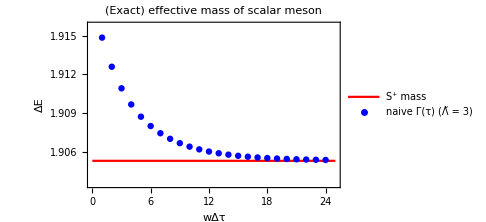

```mathematica
plotE2 = Show[gapE2Plot,
effMassE2Plot,
 PlotRange -> {{0, ntstepsE2}, {Min[effMassE2]-botPaddingE2 * rangeE2,Max[effMassE2]+topPaddingE2* rangeE2}},
PlotLabel->Style["(Exact) effective mass of scalar meson", Black, FontSize->14],
Frame->True,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
```

```mathematica
(*Export["~/Desktop/E2_gap_exact.png", plotE2, ImageResolution->500]*)
```

Different-Parity Gap

### Plot settings

```mathematica
ntstepsE1 = T/2;
topPaddingE1 = 0.10;
botPaddingE1 = 0.10;
```

### Overlaps

#### Naive operator(s)

```mathematica
Block[{M01SrcOvlapGS, M01SrcOvlapsEOddP, M01SrcOvlapsEEvenP}, 
Print[M01SrcOvlapGS = Total[M01SrcOnGS].Total[gs]//.rules];
Print[M01SrcOvlapsEEvenP = Table[Total[M01SrcOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[M01SrcOvlapsEOddP = Table[Total[M01SrcOnGS].Total[estate]//.rules, {estate, eOddP}]];
M01SrcOvlaps = Join[{M01SrcOvlapGS},M01SrcOvlapsEEvenP,M01SrcOvlapsEOddP]];
```

-1.51788×10^-17

{2.60209×10^-18,3.46945×10^-18,-7.80626×10^-18,0.,1.9082×10^-17,3.25261×10^-18,-3.46945×10^-18,1.73472×10^-18}

{0.634927,0.042445,-0.00665643,0.0501376,-0.0130753,-0.00388975}

```mathematica
Block[{M01SnkOvlapGS, M01SnkOvlapsEOddP, M01SnkOvlapsEEvenP}, 
Print[M01SnkOvlapGS = Total[M01SrcOnGS].Total[gs]//.rules];
Print[M01SnkOvlapsEEvenP = Table[Total[M01SrcOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[M01SnkOvlapsEOddP = Table[Total[M01SrcOnGS].Total[estate]//.rules, {estate, eOddP}]];
M01SnkOvlaps = Join[{M01SnkOvlapGS},M01SnkOvlapsEEvenP,M01SnkOvlapsEOddP]];
```

-1.51788×10^-17

{2.60209×10^-18,3.46945×10^-18,-7.80626×10^-18,0.,1.9082×10^-17,3.25261×10^-18,-3.46945×10^-18,1.73472×10^-18}

{0.634927,0.042445,-0.00665643,0.0501376,-0.0130753,-0.00388975}

```mathematica
Block[{M01SrcBadOvlapGS, M01SrcBadOvlapsEOddP, M01SrcBadOvlapsEEvenP}, 
Print[M01SrcBadOvlapGS = Total[M01SrcBadOnGS].Total[gs]//.rules];
Print[M01SrcBadOvlapsEEvenP = Table[Total[M01SrcBadOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[M01SrcBadOvlapsEOddP = Table[Total[M01SrcBadOnGS].Total[estate]//.rules, {estate, eOddP}]];
M01SrcBadOvlaps = Join[{M01SrcBadOvlapGS},M01SrcBadOvlapsEEvenP,M01SrcBadOvlapsEOddP]];
```

1.20346×10^-17

{0.342871,0.0394124,-0.053045,0.,0.00226207,-0.049009,0.000503316,0.00421131}

{0.287842,-0.00105907,-0.00905807,0.000611755,-0.00308975,-0.00939611}

```mathematica
Block[{M01SnkBadOvlapGS, M01SnkBadOvlapsEOddP, M01SnkBadOvlapsEEvenP}, 
Print[M01SnkBadOvlapGS = Total[M01SnkBadOnGS].Total[gs]//.rules];
Print[M01SnkBadOvlapsEEvenP = Table[Total[M01SnkBadOnGS].Total[estate]//.rules, {estate, eEvenP}]];
Print[M01SnkBadOvlapsEOddP = Table[Total[M01SnkBadOnGS].Total[estate]//.rules, {estate, eOddP}]];
M01SnkBadOvlaps = Join[{M01SnkBadOvlapGS},M01SnkBadOvlapsEEvenP,M01SnkBadOvlapsEOddP]];
```

1.45283×10^-17

{-0.342871,-0.0394124,0.053045,0.,-0.00226207,0.049009,-0.000503316,-0.00421131}

{-0.287842,0.00105907,0.00905807,-0.000611755,0.00308975,0.00939611}

#### “Smart” operator

```mathematica
Block[{SmartOpOvlapGS, SmartOpOvlapsEOddP, SmartOpOvlapsEEvenP}, 
Print[SmartOpOvlapGS = smartOpOnGS.Total[gs]//.rules];
Print[SmartOpOvlapsEEvenP = Table[smartOpOnGS.Total[estate]//.rules, {estate, eEvenP}]];
Print[SmartOpOvlapsEOddP = Table[smartOpOnGS.Total[estate]//.rules, {estate, eOddP}]];
SmartOpOvlaps = Join[{SmartOpOvlapGS},SmartOpOvlapsEEvenP,SmartOpOvlapsEOddP]];
```

6.93889×10^-18

{-1.38778×10^-17,-4.33681×10^-18,6.93889×10^-18,0.,2.77556×10^-17,1.73472×10^-18,-1.73472×10^-18,0.}

{1.,-1.47451×10^-17,-3.13638×10^-15,-1.60462×10^-16,1.70003×10^-16,1.64799×10^-17}

### Effective mass and exact gap

```mathematica
dataE1Naive =Table[g[M01SrcOvlaps,M01SnkOvlaps, energiesParitySorted, t, T], {t, Table[t0 i, {i, 1, ntstepsE1}]}];
dataE1Bad =Table[g[M01SrcBadOvlaps,M01SnkBadOvlaps, energiesParitySorted, t, T], {t, Table[t0 i, {i, 1, ntstepsE1}]}];
dataE1Smart =Table[g[SmartOpOvlaps,SmartOpOvlaps, energiesParitySorted, t, T], {t, Table[t0 i, {i, 1, ntstepsE1}]}];
```

```mathematica
gapE1 = evaluesOddPShifted⟦1⟧ - evaluesEvenPShifted⟦1⟧;
effMassE1Naive = Log[Drop[dataE1Naive, -1]/ Drop[dataE1Naive, 1]]/t0;
effMassE1Bad = Log[Drop[dataE1Bad, -1]/ Drop[dataE1Bad, 1]]/t0;
effMassE1Smart = Log[Drop[dataE1Smart, -1]/ Drop[dataE1Smart, 1]]/t0;
```

```mathematica
effMassE1Max=Max[Max[effMassE1Naive],Max[effMassE1Smart]];
effMassE1Min = Min[Min[effMassE1Naive], Min[effMassE1Smart]];
rangeE1 =effMassE1Max - effMassE1Min;
```

### Plots

Make one plot with, and one plot without the “bad” operator

```mathematica
gapE1Plot = Plot[gapE1, {x,0, ntstepsE1}, PlotStyle->Red,  PlotLegends->{"V^- mass"},LabelStyle->{FontSize->  14}];
effMassE1NaivePlot= ListPlot[effMassE1Naive,   
PlotLegends->{StringForm["naive Γ(τ)\n(Λ̃ = `1`)", Λ2]}, 
PlotStyle->Blue, LabelStyle->{FontSize->  14}];
effMassE1BadPlot= ListPlot[effMassE1Bad,   
PlotLegends->{StringForm["bad Γ(τ)\n(Λ̃ = `1`)", Λ2]}, 
PlotStyle->Orange, LabelStyle->{FontSize->  14}];
effMassE1SmartPlot= ListPlot[effMassE1Smart,  
 PlotLegends->{StringForm["smart Γ(τ)\n(Λ̃ = `1`)", Λ3]}, 
PlotStyle->Black, LabelStyle->{FontSize->  14}];
```

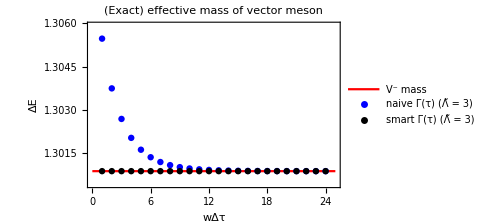

```mathematica
plotE1withoutBad= Show[gapE1Plot,effMassE1NaivePlot, effMassE1SmartPlot,
 PlotRange -> {{0, ntstepsE1}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
```

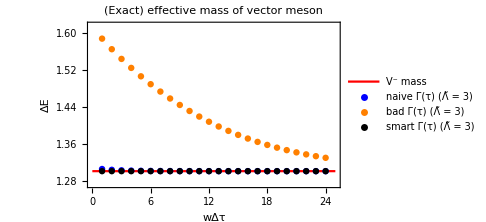

```mathematica
effMassE1Max=Max[Max[effMassE1Naive],Max[effMassE1Smart], Max[effMassE1Bad]];
effMassE1Min = Min[Min[effMassE1Naive], Min[effMassE1Smart],  Min[effMassE1Bad]];
rangeE1 =effMassE1Max - effMassE1Min;
plotE1withBad= Show[gapE1Plot,effMassE1NaivePlot,effMassE1BadPlot, effMassE1SmartPlot,
 PlotRange -> {{0, ntstepsE1}, {effMassE1Min-botPaddingE1 * rangeE1,effMassE1Max+topPaddingE1* rangeE1}},
PlotLabel->Style["(Exact) effective mass of vector meson", Black, FontSize->17],
Frame->True,
FrameLabel->{Style["wΔτ",Black, FontSize-> 20],
Style["ΔE",Black, FontSize-> 20],None,None},
FrameTicksStyle->{Directive[Black, 15], Directive[Black, 15]},
FrameStyle->Directive[Black, 15, Thickness[0.002]],
ImageSize->Medium]
```

```mathematica
(*Export["~/Desktop/E1_gap_exact_1_L2_3_L3_3.png", plotE1withoutBad, ImageResolution->500]
Export["~/Desktop/E1_gap_exact_2_L2_3_L3_3.png", plotE1withBad, ImageResolution->500]*)
```